```mathematica
SetDirectory[NotebookDirectory[]];
```

### Test with the circle

```mathematica
(******)
```

```mathematica
Sigmoid[x_]:=1/(1+Exp[-x])
```

```mathematica
ImportLayer[L_]:=Module[{W,b},W=Import["w"<>ToString[L]<>"_circle_model_squared.csv","CSV"];
b=Import["b"<>ToString[L]<>"_circle_model_squared.csv","CSV"];
{W,Transpose[b][[1]]}];
ForwardLayerSig[z_,L_]:=Module[{W,b,zNext},{W,b}=ImportLayer[L];
zNext=Transpose[W].z+b;
Sigmoid[zNext]];
ForwardLayerNoSig[z_,L_]:=Module[{W,b,zNext},{W,b}=ImportLayer[L];
zNext=Transpose[W].z+b;
zNext];
```

```mathematica
(*ForwardPropagation[z0_,layers_]:=Module[{thisa=z0,newa=0},
Do[newa=ForwardLayerSig[thisa,L];thisa=newa,{L,layers}];
newa];*)
```

```mathematica
z0={x1};
```

```mathematica
a1=ForwardLayerSig[z0,0];
```

```mathematica
a2=ForwardLayerSig[a1,1];
```

```mathematica
a3=ForwardLayerNoSig[a2,2];
```

```mathematica
a3DL8=Series[a3[[1]],{x1,0,8}]
```

0.983578+0.00676044 x1-0.999513 x1^2-0.0546026 x1^3-0.00445136 x1^4+0.0485768 x1^5+0.00377613 x1^6+0.105742 x1^7+0.000983151 x1^8+O[x1]^9

```mathematica
a3DL8p25=Series[a3[[1]],{x1,0.25,8}]
```

0.921982-0.50237 (x1-0.25)-1.03231 (x1-0.25)^2-0.014534 (x1-0.25)^3+0.108454 (x1-0.25)^4+0.154232 (x1-0.25)^5+0.0752856 (x1-0.25)^6-0.126718 (x1-0.25)^7-0.341757 (x1-0.25)^8+O[x1-0.25]^9

```mathematica
Expand[a3DL8p25//Normal]
```

0.983576+0.00680227 x1-1.00016 x1^2-0.0487544 x1^3-0.0379066 x1^4+0.174024 x1^5-0.301034 x1^6+0.556797 x1^7-0.341757 x1^8

```mathematica
a3ϵ=a3[[1]]/.x1->x1 ϵ/.x2->x2 ϵ;
```

```mathematica
a3ϵ/.ϵ->0
```

1.00021

```mathematica
Expand[D[a3ϵ,ϵ]/.ϵ->0]
```

-4.83869×10^-6 x1-0.000231228 x2

```mathematica
Expand[D[a3ϵ,{ϵ,2}]/.ϵ->0]
```

-0.0000878105 x1^2+8.91896×10^-6 x1 x2-0.000127546 x2^2

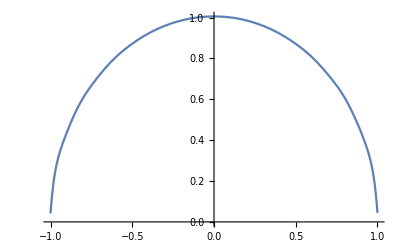

```mathematica
Plot[a3,{x0,-1,1}]
```

```mathematica
(*****)
```

### 10d potential (from Camille) : no scrambling

```mathematica
ImportLayer10d[L_]:=Module[{W,b},W=Import["w"<>ToString[L]<>"_model_10d_pot_3.csv","CSV"];
b=Import["b"<>ToString[L]<>"_model_10d_pot_3.csv","CSV"];Print[W//Dimensions,b//Dimensions];
{W,Transpose[b][[1]]}];
ForwardLayer10dSig[z_,L_]:=Module[{W,b,zNext},{W,b}=ImportLayer10d[L];
zNext=Transpose[W].z+b;
Sigmoid[zNext]];
ForwardLayer10dNoSig[z_,L_]:=Module[{W,b,zNext},{W,b}=ImportLayer10d[L];
zNext=Transpose[W].z+b;
zNext];
```

```mathematica
z0={ϵ x2,ϵ x3,ϵ x4};
```

```mathematica
a1=ForwardLayer10dSig[z0,0];
```

{3,512}{512,1}

```mathematica
a2=ForwardLayer10dSig[a1,1];
```

{512,512}{512,1}

```mathematica
a3=ForwardLayer10dNoSig[a2,2];
```

{512,1}{1,1}

```mathematica
(*a4=ForwardLayer10dNoSig[a3,2];*)
```

```mathematica
a3ϵ=a3[[1]];
```

```mathematica
(*x1+x2+x3^2+4 x4^2=0*)
```

```mathematica
a3ϵ/.ϵ->0
```

0.000117118

```mathematica
Expand[D[a3ϵ,ϵ]/.ϵ->0]
```

-1.00077 x2+0.000750563 x3-0.000182541 x4

```mathematica
Timing[1/2 Expand[D[a3ϵ,{ϵ,2}]/.ϵ->0]]//Expand
```

{29.9402,0.000568163 x2^2+0.00116303 x2 x3-0.988846 x3^2+0.001734 x2 x4+0.00947587 x3 x4-3.99526 x4^2}

```mathematica
Timing[1/(3!)Expand[D[a3ϵ,{ϵ,3}]/.ϵ->0]]//Expand
```

{37.4796,0.000631005 x2^3-0.00338104 x2^2 x3+0.00173543 x2 x3^2+0.00402771 x3^3-0.00366779 x2^2 x4+0.0129072 x2 x3 x4+0.0200967 x3^2 x4+0.00393449 x2 x4^2-0.0178203 x3 x4^2+0.0122565 x4^3}

```mathematica
Timing[1/(4!)Expand[D[a3ϵ,{ϵ,4}]/.ϵ->0]]//Expand
```

{36.4289,-0.000487563 x2^4-0.00100948 x2^3 x3+0.00818732 x2^2 x3^2-0.0071255 x2 x3^3-0.0804973 x3^4-0.00045869 x2^3 x4+0.00334336 x2^2 x3 x4-0.0451915 x2 x3^2 x4-0.074937 x3^3 x4+0.0186465 x2^2 x4^2-0.00755554 x2 x3 x4^2-0.0931749 x3^2 x4^2-0.00276212 x2 x4^3-0.0353181 x3 x4^3-0.162097 x4^4}

```mathematica
Timing[1/(5!)Expand[D[a3ϵ,{ϵ,5}]/.ϵ->0]]//Expand
```

$Aborted

### 10 d scrambled

#### Definition

```mathematica
ImportLayer10d[L_,suffixe_]:=Module[{W,b},W=Import["systematic_analysis/w"<>ToString[L]<>"_model_"<>ToString[suffixe]<>".csv","CSV"];
b=Import["systematic_analysis/b"<>ToString[L]<>"_model_"<>ToString[suffixe]<>".csv","CSV"];Print[W//Dimensions,b//Dimensions];
{W,Transpose[b][[1]]}];
ForwardLayer10dSig[z_,L_,suffixe_]:=Module[{W,b,zNext},{W,b}=ImportLayer10d[L,suffixe];
zNext=Transpose[W].z+b;
Sigmoid[zNext]];
ForwardLayer10dNoSig[z_,L_,suffixe_]:=Module[{W,b,zNext},{W,b}=ImportLayer10d[L,suffixe];
zNext=Transpose[W].z+b;
zNext];
```

```mathematica
NNres[nlayers_,nvar_,suffixe_,thisx_]:=Module[{aprev=Join[Array[x,thisx-1],Array[x,10-thisx,thisx+1]]ϵ },Do[anext=ForwardLayer10dSig[aprev,i-1,suffixe];aprev=anext,{i,nlayers-1}];
anext=ForwardLayer10dNoSig[aprev,nlayers-1,suffixe];anext]
```

#### 1st pol : x1 (x0 in python)

```mathematica
OutNN=NNres[3,9,"10d_x0_order1",1];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

-0.000384674

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{14.7557,0.570044 x[2]-0.36888 x[3]+0.578769 x[4]-0.465167 x[5]-0.122567 x[6]-0.93546 x[7]-0.355891 x[8]-0.114768 x[9]+0.0727819 x[10]}

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{10.1243,0.46779 x[2]-0.580887 x[3]+0.450157 x[4]-0.623938 x[5]-0.253952 x[6]-0.966904 x[7]-0.319453 x[8]-0.268136 x[9]+0.142732 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{38.9218,0.0372973 x[1]^2-0.0502203 x[1] x[2]+0.0176164 x[2]^2+0.0798828 x[1] x[3]-0.0553518 x[2] x[3]+0.0442793 x[3]^2-0.0624904 x[1] x[4]+0.0414623 x[2] x[4]-0.0673474 x[3] x[4]+0.027402 x[4]^2-0.00847902 x[1] x[5]+0.00731499 x[2] x[5]-0.00851893 x[3] x[5]+0.00477841 x[4] x[5]+0.00503533 x[5]^2-0.128442 x[1] x[6]+0.0882849 x[2] x[6]-0.141479 x[3] x[6]+0.107744 x[4] x[6]+0.0158262 x[5] x[6]+0.111831 x[6]^2-0.034278 x[1] x[7]+0.0252323 x[2] x[7]-0.0394347 x[3] x[7]+0.0281171 x[4] x[7]+0.00785162 x[5] x[7]+0.0613022 x[6] x[7]+0.00862562 x[7]^2+0.000527862 x[1] x[8]-0.00167211 x[2] x[8]-0.00138237 x[3] x[8]+0.00349842 x[4] x[8]-0.0131166 x[5] x[8]+0.000502017 x[6] x[8]-0.00850506 x[7] x[8]+0.00571843 x[8]^2+0.0112253 x[1] x[9]-0.00859505 x[2] x[9]+0.012722 x[3] x[9]-0.00824332 x[4] x[9]-0.00639028 x[5] x[9]-0.0184824 x[6] x[9]-0.00746098 x[7] x[9]+0.00481097 x[8] x[9]+0.00186895 x[9]^2}

#### 2nd pol : x1^2 (x0 in python)

```mathematica
OutNNx0squared=NNres[3,9,"10d_x0_squared",1];
```

Import::nffil: File systematic_analysis/w0_model_10d_x0_squared.csv not found during Import.

Import::nffil: File systematic_analysis/b0_model_10d_x0_squared.csv not found during Import.

{}{}

Import::nffil: File systematic_analysis/w1_model_10d_x0_squared.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

{}{}

{}{}

```mathematica
OutNNx0squared[[1]]/.ϵ->0
```

-0.000241262

```mathematica
Timing[Expand[D[OutNNx0squared[[1]],{ϵ,1}]/.ϵ->0]]
```

{10.1654,0.00255632 x[1]-0.00508544 x[2]+0.00134784 x[3]-0.00912008 x[4]+0.0000759949 x[5]-0.00608605 x[6]-0.00445052 x[7]+0.00171806 x[8]-0.000185514 x[9]}

```mathematica
Timing[Expand[1/(2!)D[OutNNx0squared[[1]],{ϵ,2}]/.ϵ->0]]
```

{42.9781,0.343164 x[1]^2-0.353266 x[1] x[2]+0.0911417 x[2]^2+0.611057 x[1] x[3]-0.31431 x[2] x[3]+0.272294 x[3]^2-0.419958 x[1] x[4]+0.216731 x[2] x[4]-0.373455 x[3] x[4]+0.129378 x[4]^2-0.111619 x[1] x[5]+0.0571861 x[2] x[5]-0.0992502 x[3] x[5]+0.0660361 x[4] x[5]+0.00890993 x[5]^2-0.954245 x[1] x[6]+0.490517 x[2] x[6]-0.848766 x[3] x[6]+0.582324 x[4] x[6]+0.151951 x[5] x[6]+0.65962 x[6]^2-0.474017 x[1] x[7]+0.244301 x[2] x[7]-0.422338 x[3] x[7]+0.288667 x[4] x[7]+0.0765783 x[5] x[7]+0.656714 x[6] x[7]+0.163727 x[7]^2-0.10387 x[1] x[8]+0.0530112 x[2] x[8]-0.0925236 x[3] x[8]+0.066936 x[4] x[8]+0.0155889 x[5] x[8]+0.145971 x[6] x[8]+0.0709072 x[7] x[8]+0.00993418 x[8]^2+0.019068 x[1] x[9]-0.0100419 x[2] x[9]+0.0177835 x[3] x[9]-0.0106005 x[4] x[9]-0.00366077 x[5] x[9]-0.0268522 x[6] x[9]-0.0138554 x[7] x[9]-0.00169108 x[8] x[9]+0.000595439 x[9]^2}

#### 3rd pol : x2 (x1 in python)

```mathematica
OutNNx0squared=NNres[3,9,"10d_x1_order0",2];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNNx0squared[[1]]/.ϵ->0
```

-0.00029141

```mathematica
Timing[Expand[D[OutNNx0squared[[1]],{ϵ,1}]/.ϵ->0]]
```

{15.3585,-0.270986 x[1]-0.189187 x[3]-0.267153 x[4]-1.0128 x[5]-0.135704 x[6]-0.393211 x[7]+0.0891408 x[8]-0.132025 x[9]+0.20436 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNNx0squared[[1]],{ϵ,2}]/.ϵ->0]]
```

{60.5873,0.00437952 x[1]^2+0.00296211 x[1] x[3]-0.0472737 x[3]^2+0.0148488 x[1] x[4]-0.0304994 x[3] x[4]+0.00535873 x[4]^2+0.0256294 x[1] x[5]-0.0171274 x[3] x[5]+0.032305 x[4] x[5]+0.0313908 x[5]^2-0.00770055 x[1] x[6]+0.0359019 x[3] x[6]+0.000993616 x[4] x[6]-0.0113002 x[5] x[6]-0.0047145 x[6]^2+0.0146828 x[1] x[7]-0.0125305 x[3] x[7]+0.0178015 x[4] x[7]+0.0377062 x[5] x[7]-0.00755617 x[6] x[7]+0.00915633 x[7]^2-0.00411229 x[1] x[8]+0.023379 x[3] x[8]+0.00234484 x[4] x[8]-0.00461405 x[5] x[8]-0.00679153 x[6] x[8]-0.00313436 x[7] x[8]-0.00256063 x[8]^2-0.00913323 x[1] x[9]+0.0398594 x[3] x[9]+0.00106706 x[4] x[9]-0.0144829 x[5] x[9]-0.00871649 x[6] x[9]-0.0050117 x[7] x[9]-0.00644837 x[8] x[9]-0.0057784 x[9]^2+0.00371516 x[1] x[10]-0.0163336 x[3] x[10]-0.000906728 x[4] x[10]+0.00574978 x[5] x[10]+0.00356969 x[6] x[10]+0.00243844 x[7] x[10]+0.00260514 x[8] x[10]+0.00483947 x[9] x[10]-0.00085185 x[10]^2}

#### 4th pol : x2^2(x1 in python)

```mathematica
OutNNx1squared=NNres[3,9,"10d_x1_order1",2];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNNx1squared[[1]]/.ϵ->0
```

-0.0000571495

```mathematica
Timing[Expand[D[OutNNx1squared[[1]],{ϵ,1}]/.ϵ->0]]
```

{14.6756,0.00425726 x[1]-0.00857754 x[3]-0.00109163 x[4]+0.00879444 x[5]+0.00643062 x[6]+0.00188506 x[7]+0.00837483 x[8]+0.00624716 x[9]-0.00105884 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNNx1squared[[1]],{ϵ,2}]/.ϵ->0]]
```

{55.5034,0.0654681 x[1]^2-0.214366 x[1] x[3]+0.175541 x[3]^2+0.103915 x[1] x[4]-0.169567 x[3] x[4]+0.0416308 x[4]^2+0.283381 x[1] x[5]-0.464254 x[3] x[5]+0.224499 x[4] x[5]+0.307136 x[5]^2+0.030195 x[1] x[6]-0.0495339 x[3] x[6]+0.0226881 x[4] x[6]+0.0652678 x[5] x[6]+0.00397643 x[6]^2+0.121533 x[1] x[7]-0.198541 x[3] x[7]+0.096535 x[4] x[7]+0.262759 x[5] x[7]+0.027287 x[6] x[7]+0.0564298 x[7]^2+0.0646194 x[1] x[8]-0.10631 x[3] x[8]+0.0496669 x[4] x[8]+0.140516 x[5] x[8]+0.0161838 x[6] x[8]+0.0593327 x[7] x[8]+0.0170811 x[8]^2+0.0328327 x[1] x[9]-0.0541892 x[3] x[9]+0.0254159 x[4] x[9]+0.0710112 x[5] x[9]+0.00825611 x[6] x[9]+0.0300013 x[7] x[9]+0.0172174 x[8] x[9]+0.00500576 x[9]^2+0.00242837 x[1] x[10]-0.00406627 x[3] x[10]+0.00231647 x[4] x[10]+0.00539815 x[5] x[10]+0.000434167 x[6] x[10]+0.00253878 x[7] x[10]+0.00102603 x[8] x[10]+0.000457082 x[9] x[10]-9.18172×10^-6 x[10]^2}

#### 5th pol : x3^(x2 in python)

```mathematica
OutNNx1squared=NNres[3,9,"10d_x2_order0",3];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNNx1squared[[1]]/.ϵ->0
```

0.000276637

```mathematica
Timing[Expand[D[OutNNx1squared[[1]],{ϵ,1}]/.ϵ->0]]
```

{10.5926,-0.190285 x[1]-0.208105 x[3]-0.4022 x[4]-0.967665 x[5]-0.103753 x[6]-0.286202 x[7]+0.0346858 x[8]-0.106526 x[9]+0.114594 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNNx1squared[[1]],{ϵ,2}]/.ϵ->0]]
```

{44.3041,-0.0168508 x[1]^2-0.0237421 x[1] x[3]-0.0113045 x[3]^2-0.0467355 x[1] x[4]-0.0375299 x[3] x[4]-0.0312699 x[4]^2-0.113413 x[1] x[5]-0.0963941 x[3] x[5]-0.162569 x[4] x[5]-0.211388 x[5]^2-0.0143854 x[1] x[6]-0.0235265 x[3] x[6]-0.0359394 x[4] x[6]-0.0947819 x[5] x[6]-0.0117465 x[6]^2-0.0287754 x[1] x[7]-0.0260108 x[3] x[7]-0.0408699 x[4] x[7]-0.108766 x[5] x[7]-0.0308493 x[6] x[7]-0.0138451 x[7]^2+0.00603825 x[1] x[8]-0.00308015 x[3] x[8]-0.000857672 x[4] x[8]-0.0048501 x[5] x[8]-0.00634045 x[6] x[8]-0.00510947 x[7] x[8]-0.00285231 x[8]^2-0.0369718 x[1] x[9]-0.0230144 x[3] x[9]-0.0524411 x[4] x[9]-0.120557 x[5] x[9]-0.00654923 x[6] x[9]-0.0297284 x[7] x[9]+0.0126315 x[8] x[9]-0.0183826 x[9]^2+0.0194424 x[1] x[10]+0.0188466 x[3] x[10]+0.0331137 x[4] x[10]+0.0813057 x[5] x[10]+0.0131195 x[6] x[10]+0.0238448 x[7] x[10]-0.000915921 x[8] x[10]+0.0180699 x[9] x[10]-0.00642647 x[10]^2}

#### 6th pol : (x3^)^2(x2 in python)

```mathematica
OutNN=NNres[3,9,"10d_x2_order1",3];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

-0.000283108

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{10.7703,0.00270009 x[1]+0.00167072 x[3]+0.00264381 x[4]+0.0105829 x[5]+0.00596027 x[6]-0.000270929 x[7]+0.00491366 x[8]+0.00535317 x[9]-0.00194712 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{43.4865,0.0533251 x[1]^2+0.0692758 x[1] x[3]+0.022884 x[3]^2+0.184856 x[1] x[4]+0.119531 x[3] x[4]+0.159198 x[4]^2+0.409068 x[1] x[5]+0.264024 x[3] x[5]+0.705188 x[4] x[5]+0.769093 x[5]^2+0.0308953 x[1] x[6]+0.0197674 x[3] x[6]+0.0515119 x[4] x[6]+0.113652 x[5] x[6]+0.00445277 x[6]^2+0.126349 x[1] x[7]+0.0822978 x[3] x[7]+0.217767 x[4] x[7]+0.481772 x[5] x[7]+0.0347458 x[6] x[7]+0.0747443 x[7]^2+0.00523645 x[1] x[8]+0.00328327 x[3] x[8]+0.00745179 x[4] x[8]+0.0138617 x[5] x[8]+0.0016399 x[6] x[8]+0.00471913 x[7] x[8]+0.0000942732 x[8]^2+0.0358693 x[1] x[9]+0.0223145 x[3] x[9]+0.0624534 x[4] x[9]+0.134809 x[5] x[9]+0.011039 x[6] x[9]+0.0415548 x[7] x[9]+0.00194821 x[8] x[9]+0.0068429 x[9]^2-0.0283653 x[1] x[10]-0.0186097 x[3] x[10]-0.0482242 x[4] x[10]-0.106405 x[5] x[10]-0.00791548 x[6] x[10]-0.0330702 x[7] x[10]-0.00120888 x[8] x[10]-0.00943927 x[9] x[10]+0.00371613 x[10]^2}

#### 7th pol : x4^(x2 in python)

```mathematica
OutNN=NNres[3,9,"10d_x3_order0",4];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

-0.000173823

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{11.7987,0.411834 x[1]-0.369158 x[3]-0.518019 x[4]-0.245652 x[5]-0.0968266 x[6]+0.522967 x[7]-0.172281 x[8]-0.0961539 x[9]-0.25119 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{43.921,0.054601 x[1]^2-0.0946616 x[1] x[3]+0.0411924 x[3]^2-0.135846 x[1] x[4]+0.117868 x[3] x[4]+0.0849263 x[4]^2-0.05796 x[1] x[5]+0.0505256 x[3] x[5]+0.0709889 x[4] x[5]+0.0167656 x[5]^2-0.0235097 x[1] x[6]+0.0199807 x[3] x[6]+0.0296497 x[4] x[6]+0.0109552 x[5] x[6]+0.00278246 x[6]^2+0.127393 x[1] x[7]-0.110387 x[3] x[7]-0.158222 x[4] x[7]-0.0675813 x[5] x[7]-0.0263568 x[6] x[7]+0.0734746 x[7]^2-0.0319294 x[1] x[8]+0.0274813 x[3] x[8]+0.0394532 x[4] x[8]+0.0161914 x[5] x[8]+0.0066739 x[6] x[8]-0.0354342 x[7] x[8]+0.00393425 x[8]^2-0.0432177 x[1] x[9]+0.0380361 x[3] x[9]+0.0542683 x[4] x[9]+0.0240641 x[5] x[9]+0.0106735 x[6] x[9]-0.0536228 x[7] x[9]+0.0154231 x[8] x[9]+0.00567736 x[9]^2-0.0668953 x[1] x[10]+0.0578748 x[3] x[10]+0.0832507 x[4] x[10]+0.0357825 x[5] x[10]+0.014916 x[6] x[10]-0.0786479 x[7] x[10]+0.0197749 x[8] x[10]+0.0252358 x[9] x[10]+0.0202406 x[10]^2}

#### 8th pol : (x5^3)^(x2 in python)

```mathematica
OutNN=NNres[3,9,"10d_x4_order3",5];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

-0.0000574884

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{10.5771,-0.0000224084 x[1]-0.0000413467 x[2]+0.0000316668 x[3]-0.0000201698 x[4]-0.0000416172 x[6]-8.6229×10^-6 x[7]-0.0000299744 x[8]+0.0000367749 x[9]+0.0000522679 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{44.9504,3.04714×10^-6 x[1]^2-0.0000975934 x[1] x[2]+0.000495835 x[2]^2-0.0000445654 x[1] x[3]+0.000508422 x[2] x[3]+0.000124849 x[3]^2+5.95879×10^-6 x[1] x[4]-0.0000887239 x[2] x[4]-0.0000405825 x[3] x[4]+2.21345×10^-6 x[4]^2+0.000017592 x[1] x[6]-0.000223052 x[2] x[6]-0.000105271 x[3] x[6]+0.0000163477 x[4] x[6]+0.000019928 x[6]^2-0.0000509594 x[1] x[7]+0.000528425 x[2] x[7]+0.000268617 x[3] x[7]-0.0000464591 x[4] x[7]-0.000115964 x[6] x[7]+0.000139928 x[7]^2-0.0000632846 x[1] x[8]+0.000644605 x[2] x[8]+0.00033052 x[3] x[8]-0.0000574355 x[4] x[8]-0.000145439 x[6] x[8]+0.000343536 x[7] x[8]+0.000208805 x[8]^2+0.0000165247 x[1] x[9]-0.000141935 x[2] x[9]-0.0000779949 x[3] x[9]+0.0000148401 x[4] x[9]+0.0000377426 x[6] x[9]-0.0000769634 x[7] x[9]-0.000091543 x[8] x[9]+7.9267×10^-6 x[9]^2+0.0000337197 x[1] x[10]-0.000306939 x[2] x[10]-0.000164404 x[3] x[10]+0.0000306678 x[4] x[10]+0.0000757042 x[6] x[10]-0.00016521 x[7] x[10]-0.000198626 x[8] x[10]+0.000039715 x[9] x[10]+0.0000442478 x[10]^2}

```mathematica
Timing[Expand[1/(3!)D[OutNN[[1]],{ϵ,3}]/.ϵ->0]]
```

{229.218,-2.68929×10^-7 x[1]^3+0.0000131861 x[1]^2 x[2]-0.000190871 x[1] x[2]^2+0.000848738 x[2]^3+5.92545×10^-6 x[1]^2 x[3]-0.000174208 x[1] x[2] x[3]+0.00118755 x[2]^2 x[3]-0.0000396796 x[1] x[3]^2+0.000550347 x[2] x[3]^2+0.0000846163 x[3]^3-7.6345×10^-7 x[1]^2 x[4]+0.0000238498 x[1] x[2] x[4]-0.000172624 x[2]^2 x[4]+0.0000108025 x[1] x[3] x[4]-0.000157432 x[2] x[3] x[4]-0.0000359238 x[3]^2 x[4]-6.49658×10^-7 x[1] x[4]^2+0.0000105561 x[2] x[4]^2+4.73004×10^-6 x[3] x[4]^2-1.79789×10^-7 x[4]^3-2.34791×10^-6 x[1]^2 x[6]+0.0000675362 x[1] x[2] x[6]-0.000465254 x[2]^2 x[6]+0.0000308598 x[1] x[3] x[6]-0.000428524 x[2] x[3] x[6]-0.0000983455 x[3]^2 x[6]-4.44295×10^-6 x[1] x[4] x[6]+0.0000612444 x[2] x[4] x[6]+0.0000280117 x[3] x[4] x[6]-1.88973×10^-6 x[4]^2 x[6]-5.79519×10^-6 x[1] x[6]^2+0.0000811417 x[2] x[6]^2+0.0000372098 x[3] x[6]^2-5.18812×10^-6 x[4] x[6]^2-4.64095×10^-6 x[6]^3+6.87747×10^-6 x[1]^2 x[7]-0.000198681 x[1] x[2] x[7]+0.00132802 x[2]^2 x[7]-0.0000906764 x[1] x[3] x[7]+0.00123739 x[2] x[3] x[7]+0.000286462 x[3]^2 x[7]+0.0000125775 x[1] x[4] x[7]-0.000179471 x[2] x[4] x[7]-0.0000818956 x[3] x[4] x[7]+5.48845×10^-6 x[4]^2 x[7]+0.0000348764 x[1] x[6] x[7]-0.000482492 x[2] x[6] x[7]-0.000222124 x[3] x[6] x[7]+0.0000315322 x[4] x[6] x[7]+0.0000420166 x[6]^2 x[7]-0.0000515582 x[1] x[7]^2+0.000691957 x[2] x[7]^2+0.000321924 x[3] x[7]^2-0.00004651 x[4] x[7]^2-0.000125044 x[6] x[7]^2+0.000120082 x[7]^3+8.50584×10^-6 x[1]^2 x[8]-0.000248429 x[1] x[2] x[8]+0.00165659 x[2]^2 x[8]-0.000113257 x[1] x[3] x[8]+0.00154606 x[2] x[3] x[8]+0.000358426 x[3]^2 x[8]+0.0000152884 x[1] x[4] x[8]-0.000224708 x[2] x[4] x[8]-0.000102452 x[3] x[4] x[8]+6.77109×10^-6 x[4]^2 x[8]+0.0000439085 x[1] x[6] x[8]-0.000606186 x[2] x[6] x[8]-0.000279048 x[3] x[6] x[8]+0.000039888 x[4] x[6] x[8]+0.0000528174 x[6]^2 x[8]-0.000129337 x[1] x[7] x[8]+0.0017285 x[2] x[7] x[8]+0.000805615 x[3] x[7] x[8]-0.000116906 x[4] x[7] x[8]-0.000314386 x[6] x[7] x[8]+0.000450467 x[7]^2 x[8]-0.0000807251 x[1] x[8]^2+0.00107792 x[2] x[8]^2+0.00050316 x[3] x[8]^2-0.0000730105 x[4] x[8]^2-0.000197469 x[6] x[8]^2+0.000562555 x[7] x[8]^2+0.000233786 x[8]^3-2.26978×10^-6 x[1]^2 x[9]+0.0000656258 x[1] x[2] x[9]-0.000427165 x[2]^2 x[9]+0.0000299089 x[1] x[3] x[9]-0.000401922 x[2] x[3] x[9]-0.0000937068 x[3]^2 x[9]-4.08668×10^-6 x[1] x[4] x[9]+0.0000591722 x[2] x[4] x[9]+0.0000271336 x[3] x[4] x[9]-1.86339×10^-6 x[4]^2 x[9]-0.0000116556 x[1] x[6] x[9]+0.000160127 x[2] x[6] x[9]+0.000073726 x[3] x[6] x[9]-0.0000106863 x[4] x[6] x[9]-0.0000138983 x[6]^2 x[9]+0.0000341014 x[1] x[7] x[9]-0.000446302 x[2] x[7] x[9]-0.000209504 x[3] x[7] x[9]+0.000030752 x[4] x[7] x[9]+0.0000830239 x[6] x[7] x[9]-0.000116488 x[7]^2 x[9]+0.0000426282 x[1] x[8] x[9]-0.000554876 x[2] x[8] x[9]-0.000261319 x[3] x[8] x[9]+0.000038519 x[4] x[8] x[9]+0.000104372 x[6] x[8] x[9]-0.000289999 x[7] x[8] x[9]-0.000180206 x[8]^2 x[9]-5.57313×10^-6 x[1] x[9]^2+0.0000701044 x[2] x[9]^2+0.0000334725 x[3] x[9]^2-5.03329×10^-6 x[4] x[9]^2-0.0000137355 x[6] x[9]^2+0.0000367152 x[7] x[9]^2+0.0000454008 x[8] x[9]^2-3.75008×10^-6 x[9]^3-4.6096×10^-6 x[1]^2 x[10]+0.000133211 x[1] x[2] x[10]-0.000871018 x[2]^2 x[10]+0.000060835 x[1] x[3] x[10]-0.000818278 x[2] x[3] x[10]-0.000190597 x[3]^2 x[10]-8.28081×10^-6 x[1] x[4] x[10]+0.00012092 x[2] x[4] x[10]+0.0000552502 x[3] x[4] x[10]-3.75137×10^-6 x[4]^2 x[10]-0.0000234193 x[1] x[6] x[10]+0.000323285 x[2] x[6] x[10]+0.000148941 x[3] x[6] x[10]-0.0000213193 x[4] x[6] x[10]-0.0000283445 x[6]^2 x[10]+0.0000693375 x[1] x[7] x[10]-0.000909733 x[2] x[7] x[10]-0.000426514 x[3] x[7] x[10]+0.000062893 x[4] x[7] x[10]+0.000167738 x[6] x[7] x[10]-0.000237447 x[7]^2 x[10]+0.0000866206 x[1] x[8] x[10]-0.00113345 x[2] x[8] x[10]-0.000532699 x[3] x[8] x[10]+0.0000786503 x[4] x[8] x[10]+0.000210565 x[6] x[8] x[10]-0.000592184 x[7] x[8] x[10]-0.000368788 x[8]^2 x[10]-0.0000230181 x[1] x[9] x[10]+0.00028921 x[2] x[9] x[10]+0.000137711 x[3] x[9] x[10]-0.0000209417 x[4] x[9] x[10]-0.000055448 x[6] x[9] x[10]+0.000151346 x[7] x[9] x[10]+0.000188024 x[8] x[9] x[10]-0.0000234248 x[9]^2 x[10]-0.0000231656 x[1] x[10]^2+0.000295631 x[2] x[10]^2+0.000140038 x[3] x[10]^2-0.0000210803 x[4] x[10]^2-0.0000559451 x[6] x[10]^2+0.000154739 x[7] x[10]^2+0.000192257 x[8] x[10]^2-0.0000484371 x[9] x[10]^2-0.0000331291 x[10]^3}

```mathematica
Timing[Expand[1/(4!)D[OutNN[[1]],{ϵ,4}]/.ϵ->0]]
```

$Aborted

#### 9th pol : (x5^4)^(x4 in python)

```mathematica
OutNN=NNres[3,9,"10d_x4_order4",5];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

0.0000439705

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{10.6253,-6.89711×10^-6 x[1]-5.92419×10^-6 x[2]+2.49172×10^-6 x[3]+0.0000209597 x[4]+0.0000509722 x[6]-8.58348×10^-6 x[7]-0.0000132924 x[8]-0.00003344 x[9]+4.96677×10^-7 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{42.5556,3.81635×10^-7 x[1]^2-6.2368×10^-6 x[1] x[2]-0.0000515005 x[2]^2-2.37123×10^-6 x[1] x[3]-0.000025932 x[2] x[3]-2.60402×10^-6 x[3]^2+5.79359×10^-7 x[1] x[4]+7.6729×10^-6 x[2] x[4]+1.44892×10^-6 x[3] x[4]+1.41394×10^-6 x[4]^2-2.51849×10^-6 x[1] x[6]-0.0000165248 x[2] x[6]-3.18502×10^-6 x[3] x[6]+6.22511×10^-6 x[4] x[6]+4.93401×10^-6 x[6]^2-2.148×10^-6 x[1] x[7]-0.0000418187 x[2] x[7]-0.0000109749 x[3] x[7]+2.99372×10^-6 x[4] x[7]-8.14859×10^-6 x[6] x[7]-8.17426×10^-6 x[7]^2-5.19689×10^-6 x[1] x[8]-0.0000800505 x[2] x[8]-0.0000194228 x[3] x[8]+4.44833×10^-6 x[4] x[8]-0.0000149937 x[6] x[8]-0.0000324 x[7] x[8]-0.0000303035 x[8]^2+5.71979×10^-6 x[1] x[9]+0.0000624285 x[2] x[9]+0.0000140627 x[3] x[9]-7.03498×10^-6 x[4] x[9]+1.48989×10^-6 x[6] x[9]+0.0000265727 x[7] x[9]+0.0000490639 x[8] x[9]-0.0000149741 x[9]^2+3.80152×10^-6 x[1] x[10]+0.0000495341 x[2] x[10]+0.0000115188 x[3] x[10]-3.00891×10^-6 x[4] x[10]+7.52505×10^-6 x[6] x[10]+0.0000203137 x[7] x[10]+0.000037778 x[8] x[10]-0.0000284673 x[9] x[10]-0.0000113206 x[10]^2}

```mathematica
Timing[Expand[1/(3!)D[OutNN[[1]],{ϵ,3}]/.ϵ->0]]
```

{219.155,7.36155×10^-9 x[1]^3-8.1723×10^-8 x[1]^2 x[2]-3.60493×10^-6 x[1] x[2]^2-0.0000250942 x[2]^3-3.72413×10^-8 x[1]^2 x[3]-2.1344×10^-6 x[1] x[2] x[3]-0.0000193625 x[2]^2 x[3]-2.93758×10^-7 x[1] x[3]^2-4.76727×10^-6 x[2] x[3]^2-3.77142×10^-7 x[3]^3-2.29126×10^-8 x[1]^2 x[4]+2.00008×10^-7 x[1] x[2] x[4]+5.13419×10^-7 x[2]^2 x[4]-1.35125×10^-8 x[1] x[3] x[4]+1.68161×10^-7 x[2] x[3] x[4]+1.92284×10^-8 x[3]^2 x[4]+3.9027×10^-8 x[1] x[4]^2+4.9735×10^-7 x[2] x[4]^2+1.29614×10^-7 x[3] x[4]^2+9.2175×10^-9 x[4]^3-6.38946×10^-8 x[1]^2 x[6]-2.48917×10^-6 x[1] x[2] x[6]-0.0000235626 x[2]^2 x[6]-7.63272×10^-7 x[1] x[3] x[6]-0.0000118374 x[2] x[3] x[6]-1.40479×10^-6 x[3]^2 x[6]+1.3442×10^-7 x[1] x[4] x[6]+1.88834×10^-6 x[2] x[4] x[6]+4.16664×10^-7 x[3] x[4] x[6]+2.8855×10^-7 x[4]^2 x[6]-4.03354×10^-7 x[1] x[6]^2-5.58474×10^-6 x[2] x[6]^2-1.30806×10^-6 x[3] x[6]^2+8.33305×10^-7 x[4] x[6]^2+1.36073×10^-8 x[6]^3+1.5382×10^-9 x[1]^2 x[7]-2.70246×10^-6 x[1] x[2] x[7]-0.000029329 x[2]^2 x[7]-8.20093×10^-7 x[1] x[3] x[7]-0.0000153078 x[2] x[3] x[7]-1.92983×10^-6 x[3]^2 x[7]-2.42874×10^-8 x[1] x[4] x[7]+5.39657×10^-7 x[2] x[4] x[7]+1.1521×10^-7 x[3] x[4] x[7]+1.52956×10^-7 x[4]^2 x[7]-9.55208×10^-7 x[1] x[6] x[7]-0.0000186443 x[2] x[6] x[7]-4.80868×10^-6 x[3] x[6] x[7]+8.07811×10^-7 x[4] x[6] x[7]-2.31092×10^-6 x[6]^2 x[7]-4.97007×10^-7 x[1] x[7]^2-0.0000114 x[2] x[7]^2-3.00599×10^-6 x[3] x[7]^2+5.9862×10^-8 x[4] x[7]^2-3.73002×10^-6 x[6] x[7]^2-1.47915×10^-6 x[7]^3-4.9788×10^-8 x[1]^2 x[8]-5.53401×10^-6 x[1] x[2] x[8]-0.0000559323 x[2]^2 x[8]-1.59539×10^-6 x[1] x[3] x[8]-0.0000284718 x[2] x[3] x[8]-3.46477×10^-6 x[3]^2 x[8]+1.04064×10^-7 x[1] x[4] x[8]+3.56825×10^-7 x[2] x[4] x[8]+1.89516×10^-8 x[3] x[4] x[8]+3.19938×10^-7 x[4]^2 x[8]-1.92211×10^-6 x[1] x[6] x[8]-0.0000356055 x[2] x[6] x[8]-8.84019×10^-6 x[3] x[6] x[8]+1.12146×10^-6 x[4] x[6] x[8]-4.51745×10^-6 x[6]^2 x[8]-2.09975×10^-6 x[1] x[7] x[8]-0.000043696 x[2] x[7] x[8]-0.0000112909 x[3] x[7] x[8]+2.70383×10^-7 x[4] x[7] x[8]-0.0000140991 x[6] x[7] x[8]-8.48538×10^-6 x[7]^2 x[8]-2.08941×10^-6 x[1] x[8]^2-0.0000413913 x[2] x[8]^2-0.0000104373 x[3] x[8]^2-2.22781×10^-8 x[4] x[8]^2-0.000013472 x[6] x[8]^2-0.0000161476 x[7] x[8]^2-0.0000101738 x[8]^3+9.27892×10^-8 x[1]^2 x[9]+5.62178×10^-6 x[1] x[2] x[9]+0.0000529759 x[2]^2 x[9]+1.61118×10^-6 x[1] x[3] x[9]+0.0000267144 x[2] x[3] x[9]+3.2207×10^-6 x[3]^2 x[9]-1.0557×10^-7 x[1] x[4] x[9]-1.50725×10^-6 x[2] x[4] x[9]-3.64713×10^-7 x[3] x[4] x[9]-3.86211×10^-7 x[4]^2 x[9]+1.94812×10^-6 x[1] x[6] x[9]+0.0000307543 x[2] x[6] x[9]+7.38458×10^-6 x[3] x[6] x[9]-1.98447×10^-6 x[4] x[6] x[9]+2.68854×10^-6 x[6]^2 x[9]+2.13273×10^-6 x[1] x[7] x[9]+0.0000417377 x[2] x[7] x[9]+0.0000106609 x[3] x[7] x[9]-7.04017×10^-7 x[4] x[7] x[9]+0.0000124824 x[6] x[7] x[9]+8.19352×10^-6 x[7]^2 x[9]+4.24407×10^-6 x[1] x[8] x[9]+0.0000788658 x[2] x[8] x[9]+0.0000197009 x[3] x[8] x[9]-7.49394×10^-7 x[4] x[8] x[9]+0.0000236013 x[6] x[8] x[9]+0.0000310243 x[7] x[8] x[9]+0.0000292613 x[8]^2 x[9]-2.25781×10^-6 x[1] x[9]^2-0.0000362062 x[2] x[9]^2-8.83623×10^-6 x[3] x[9]^2+9.60633×10^-7 x[4] x[9]^2-9.31568×10^-6 x[6] x[9]^2-0.0000145012 x[7] x[9]^2-0.000027068 x[8] x[9]^2+7.93566×10^-6 x[9]^3+3.23178×10^-8 x[1]^2 x[10]+3.66039×10^-6 x[1] x[2] x[10]+0.0000358314 x[2]^2 x[10]+1.05256×10^-6 x[1] x[3] x[10]+0.0000180504 x[2] x[3] x[10]+2.14123×10^-6 x[3]^2 x[10]-3.33804×10^-8 x[1] x[4] x[10]-1.99625×10^-7 x[2] x[4] x[10]-7.25404×10^-8 x[3] x[4] x[10]-2.20134×10^-7 x[4]^2 x[10]+1.31783×10^-6 x[1] x[6] x[10]+0.000022436 x[2] x[6] x[10]+5.35929×10^-6 x[3] x[6] x[10]-8.29346×10^-7 x[4] x[6] x[10]+2.64959×10^-6 x[6]^2 x[10]+1.37092×10^-6 x[1] x[7] x[10]+0.0000280611 x[2] x[7] x[10]+7.19993×10^-6 x[3] x[7] x[10]-2.0915×10^-7 x[4] x[7] x[10]+8.89136×10^-6 x[6] x[7] x[10]+5.46191×10^-6 x[7]^2 x[10]+2.7996×10^-6 x[1] x[8] x[10]+0.00005303 x[2] x[8] x[10]+0.0000131941 x[3] x[8] x[10]+6.51431×10^-9 x[4] x[8] x[10]+0.000016948 x[6] x[8] x[10]+0.0000207531 x[7] x[8] x[10]+0.000019563 x[8]^2 x[10]-2.86783×10^-6 x[1] x[9] x[10]-0.0000499517 x[2] x[9] x[10]-0.0000122162 x[3] x[9] x[10]+5.59213×10^-7 x[4] x[9] x[10]-0.0000144004 x[6] x[9] x[10]-0.0000197788 x[7] x[9] x[10]-0.0000370641 x[8] x[9] x[10]+0.0000168444 x[9]^2 x[10]-9.25909×10^-7 x[1] x[10]^2-0.0000169594 x[2] x[10]^2-4.11804×10^-6 x[3] x[10]^2-1.48411×10^-8 x[4] x[10]^2-5.3281×10^-6 x[6] x[10]^2-6.64486×10^-6 x[7] x[10]^2-0.0000124942 x[8] x[10]^2+0.0000117036 x[9] x[10]^2+2.65383×10^-6 x[10]^3}

```mathematica
(*Timing[Expand[1/(4!)D[OutNN[[1]],{ϵ,4}]/.ϵ->0]]*)
```

#### 10th pol : x6^(x5 in python)

```mathematica
OutNN=NNres[3,9,"10d_x5_order0",6];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

-0.000656809

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{11.1204,-0.217168 x[1]-0.0165878 x[2]-0.242353 x[3]-0.431624 x[4]+0.383906 x[5]-0.0479535 x[7]-0.294449 x[8]-0.999626 x[9]+0.176059 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{44.7516,-0.00373746 x[1]^2-0.00024584 x[1] x[2]-0.000144328 x[2]^2-0.0378412 x[1] x[3]-0.00828992 x[2] x[3]-0.0102255 x[3]^2-0.0251867 x[1] x[4]-0.000250536 x[2] x[4]-0.0759399 x[3] x[4]-0.033062 x[4]^2+0.0504726 x[1] x[5]+0.00950267 x[2] x[5]+0.058875 x[3] x[5]+0.10366 x[4] x[5]-0.054275 x[5]^2+0.0105474 x[1] x[7]+0.00256723 x[2] x[7]-0.0036855 x[3] x[7]+0.0190912 x[4] x[7]-0.00537289 x[5] x[7]+0.00433333 x[7]^2-0.00989601 x[1] x[8]-0.00246608 x[2] x[8]-0.0240028 x[3] x[8]-0.0255729 x[4] x[8]+0.0401829 x[5] x[8]+0.0123452 x[7] x[8]+0.000910678 x[8]^2-0.0479117 x[1] x[9]-0.00455555 x[2] x[9]-0.149106 x[3] x[9]-0.127122 x[4] x[9]+0.211672 x[5] x[9]+0.0454596 x[7] x[9]-0.0378424 x[8] x[9]-0.113667 x[9]^2+0.00883371 x[1] x[10]+0.000457864 x[2] x[10]+0.0269262 x[3] x[10]+0.024318 x[4] x[10]-0.0384069 x[5] x[10]-0.00742928 x[7] x[10]+0.00797169 x[8] x[10]+0.046211 x[9] x[10]-0.00407764 x[10]^2}

#### 11th pol : x7^(x6 in python)

```mathematica
OutNN=NNres[3,9,"10d_x6_order0",7];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

0.0000885183

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{11.0231,-0.830472 x[1]+0.396968 x[2]-0.482219 x[3]+0.730489 x[4]-0.552013 x[5]-0.0152799 x[6]+0.0657684 x[8]-0.0129223 x[9]+0.283087 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{45.0667,-0.0489379 x[1]^2+0.0275475 x[1] x[2]-0.00197085 x[2]^2-0.0452107 x[1] x[3]+0.0104209 x[2] x[3]-0.00936148 x[3]^2+0.0926366 x[1] x[4]-0.0266733 x[2] x[4]+0.0431806 x[3] x[4]-0.0438125 x[4]^2-0.157443 x[1] x[5]+0.0619689 x[2] x[5]-0.0848626 x[3] x[5]+0.143185 x[4] x[5]-0.0813364 x[5]^2-0.00765634 x[1] x[6]+0.00340041 x[2] x[6]-0.00348617 x[3] x[6]+0.00694486 x[4] x[6]-0.00900818 x[5] x[6]+0.00057115 x[6]^2-0.0136384 x[1] x[8]+0.0082348 x[2] x[8]-0.00868674 x[3] x[8]+0.0123621 x[4] x[8]-0.00314265 x[5] x[8]+0.00112201 x[6] x[8]+0.00177062 x[8]^2-0.00813918 x[1] x[9]+0.00327721 x[2] x[9]-0.00564089 x[3] x[9]+0.00723028 x[4] x[9]-0.004064 x[5] x[9]-0.00250735 x[6] x[9]-0.00128761 x[8] x[9]+0.00166488 x[9]^2+0.0458498 x[1] x[10]-0.0158151 x[2] x[10]+0.0222622 x[3] x[10]-0.042674 x[4] x[10]+0.0637052 x[5] x[10]+0.0016283 x[6] x[10]+0.00269648 x[8] x[10]+0.00491774 x[9] x[10]-0.00944292 x[10]^2}

#### 12th pol : x8^(x7 in python)

```mathematica
OutNN=NNres[3,9,"10d_x7_order0",8];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

2.81755×10^-6

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{10.9939,-0.390365 x[1]+0.353651 x[2]+0.145877 x[3]-0.440555 x[4]+0.0353575 x[5]-0.220366 x[6]+0.138499 x[7]-0.218501 x[9]-0.509067 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{44.7947,0.0220271 x[1]^2-0.0508413 x[1] x[2]+0.0273958 x[2]^2-0.00768818 x[1] x[3]+0.011772 x[2] x[3]-0.00117653 x[3]^2+0.0498542 x[1] x[4]-0.0565556 x[2] x[4]-0.00758707 x[3] x[4]+0.0272235 x[4]^2-0.0387011 x[1] x[5]+0.0345696 x[2] x[5]+0.0172407 x[3] x[5]-0.0456225 x[4] x[5]-0.00201419 x[5]^2+0.0337467 x[1] x[6]-0.034503 x[2] x[6]-0.00969083 x[3] x[6]+0.0374816 x[4] x[6]-0.0199435 x[5] x[6]+0.0124295 x[6]^2-0.00577033 x[1] x[7]+0.00850161 x[2] x[7]-0.000943592 x[3] x[7]-0.00633084 x[4] x[7]+0.0133502 x[5] x[7]-0.00853929 x[6] x[7]-0.000243093 x[7]^2+0.0332868 x[1] x[9]-0.0386765 x[2] x[9]-0.00614402 x[3] x[9]+0.037685 x[4] x[9]-0.0238856 x[5] x[9]+0.020589 x[6] x[9]-0.00348711 x[7] x[9]+0.0146338 x[9]^2+0.0557048 x[1] x[10]-0.0649348 x[2] x[10]-0.0103166 x[3] x[10]+0.0623179 x[4] x[10]-0.0487472 x[5] x[10]+0.0400196 x[6] x[10]-0.00529009 x[7] x[10]+0.0467782 x[9] x[10]+0.036282 x[10]^2}

```mathematica
Timing[Expand[1/(3!)D[OutNN[[1]],{ϵ,3}]/.ϵ->0]]
```

{253.999,-0.0914252 x[1]^3+0.245398 x[1]^2 x[2]-0.215695 x[1] x[2]^2+0.0618177 x[2]^3+0.0997088 x[1]^2 x[3]-0.177891 x[1] x[2] x[3]+0.0777082 x[2]^2 x[3]-0.0330886 x[1] x[3]^2+0.0295994 x[2] x[3]^2+0.00285134 x[3]^3-0.308735 x[1]^2 x[4]+0.546998 x[1] x[2] x[4]-0.237164 x[2]^2 x[4]+0.221503 x[1] x[3] x[4]-0.195308 x[2] x[3] x[4]-0.0356979 x[3]^2 x[4]-0.339972 x[1] x[4]^2+0.295994 x[2] x[4]^2+0.119266 x[3] x[4]^2-0.119816 x[4]^3+0.0308816 x[1]^2 x[5]-0.0559799 x[1] x[2] x[5]+0.0251385 x[2]^2 x[5]-0.0312897 x[1] x[3] x[5]+0.0277262 x[2] x[3] x[5]+0.00874655 x[3]^2 x[5]+0.0720011 x[1] x[4] x[5]-0.0640615 x[2] x[4] x[5]-0.0364596 x[3] x[4] x[5]+0.040852 x[4]^2 x[5]+0.0101849 x[1] x[5]^2-0.00900498 x[2] x[5]^2-0.00536423 x[3] x[5]^2+0.0108397 x[4] x[5]^2-0.000379431 x[5]^3-0.151664 x[1]^2 x[6]+0.267834 x[1] x[2] x[6]-0.115787 x[2]^2 x[6]+0.112647 x[1] x[3] x[6]-0.0986815 x[2] x[3] x[6]-0.0200833 x[3]^2 x[6]-0.336385 x[1] x[4] x[6]+0.292409 x[2] x[4] x[6]+0.123499 x[3] x[4] x[6]-0.180328 x[4]^2 x[6]+0.0293793 x[1] x[5] x[6]-0.0266349 x[2] x[5] x[6]-0.0125368 x[3] x[5] x[6]+0.0327378 x[4] x[5] x[6]+0.00283976 x[5]^2 x[6]-0.0816563 x[1] x[6]^2+0.0710001 x[2] x[6]^2+0.0300153 x[3] x[6]^2-0.0881889 x[4] x[6]^2+0.00835885 x[5] x[6]^2-0.01453 x[6]^3+0.10203 x[1]^2 x[7]-0.181141 x[1] x[2] x[7]+0.0789917 x[2]^2 x[7]-0.0740649 x[1] x[3] x[7]+0.0651637 x[2] x[3] x[7]+0.0123122 x[3]^2 x[7]+0.228577 x[1] x[4] x[7]-0.201077 x[2] x[4] x[7]-0.0819767 x[3] x[4] x[7]+0.1251 x[4]^2 x[7]-0.0221786 x[1] x[5] x[7]+0.0207925 x[2] x[5] x[7]+0.0113286 x[3] x[5] x[7]-0.0253502 x[4] x[5] x[7]-0.00369068 x[5]^2 x[7]+0.113784 x[1] x[6] x[7]-0.100055 x[2] x[6] x[7]-0.042161 x[3] x[6] x[7]+0.125614 x[4] x[6] x[7]-0.0106239 x[5] x[6] x[7]+0.0310323 x[6]^2 x[7]-0.0370621 x[1] x[7]^2+0.0325739 x[2] x[7]^2+0.0133393 x[3] x[7]^2-0.0413559 x[4] x[7]^2+0.00426632 x[5] x[7]^2-0.0209208 x[6] x[7]^2+0.00437786 x[7]^3-0.151779 x[1]^2 x[9]+0.275855 x[1] x[2] x[9]-0.123458 x[2]^2 x[9]+0.105731 x[1] x[3] x[9]-0.0966784 x[2] x[3] x[9]-0.0156961 x[3]^2 x[9]-0.34694 x[1] x[4] x[9]+0.314736 x[2] x[4] x[9]+0.119931 x[3] x[4] x[9]-0.198356 x[4]^2 x[9]+0.0459195 x[1] x[5] x[9]-0.0418579 x[2] x[5] x[9]-0.0246185 x[3] x[5] x[9]+0.0548604 x[4] x[5] x[9]+0.00833545 x[5]^2 x[9]-0.169446 x[1] x[6] x[9]+0.152188 x[2] x[6] x[9]+0.0626843 x[3] x[6] x[9]-0.194133 x[4] x[6] x[9]+0.0189153 x[5] x[6] x[9]-0.0447482 x[6]^2 x[9]+0.11063 x[1] x[7] x[9]-0.0993287 x[2] x[7] x[9]-0.0384376 x[3] x[7] x[9]+0.126452 x[4] x[7] x[9]-0.0162673 x[5] x[7] x[9]+0.0618268 x[6] x[7] x[9]-0.0193845 x[7]^2 x[9]-0.0821164 x[1] x[9]^2+0.0751728 x[2] x[9]^2+0.0260222 x[3] x[9]^2-0.0913774 x[4] x[9]^2+0.0176546 x[5] x[9]^2-0.0474621 x[6] x[9]^2+0.029873 x[7] x[9]^2-0.0141651 x[9]^3-0.363667 x[1]^2 x[10]+0.648406 x[1] x[2] x[10]-0.284314 x[2]^2 x[10]+0.26292 x[1] x[3] x[10]-0.233944 x[2] x[3] x[10]-0.0436217 x[3]^2 x[10]-0.822851 x[1] x[4] x[10]+0.729417 x[2] x[4] x[10]+0.295553 x[3] x[4] x[10]-0.460939 x[4]^2 x[10]+0.0865858 x[1] x[5] x[10]-0.0786566 x[2] x[5] x[10]-0.0429146 x[3] x[5] x[10]+0.100511 x[4] x[5] x[10]+0.0132416 x[5]^2 x[10]-0.401924 x[1] x[6] x[10]+0.354488 x[2] x[6] x[10]+0.148688 x[3] x[6] x[10]-0.451329 x[4] x[6] x[10]+0.0411872 x[5] x[6] x[10]-0.108364 x[6]^2 x[10]+0.269573 x[1] x[7] x[10]-0.238224 x[2] x[7] x[10]-0.0970162 x[3] x[7] x[10]+0.304492 x[4] x[7] x[10]-0.0316068 x[5] x[7] x[10]+0.150406 x[6] x[7] x[10]-0.0486952 x[7]^2 x[10]-0.39686 x[1] x[9] x[10]+0.356833 x[2] x[9] x[10]+0.13682 x[3] x[9] x[10]-0.447346 x[4] x[9] x[10]+0.0622056 x[5] x[9] x[10]-0.219035 x[6] x[9] x[10]+0.143595 x[7] x[9] x[10]-0.108588 x[9]^2 x[10]-0.474937 x[1] x[10]^2+0.420443 x[2] x[10]^2+0.169936 x[3] x[10]^2-0.535155 x[4] x[10]^2+0.0598367 x[5] x[10]^2-0.260809 x[6] x[10]^2+0.17484 x[7] x[10]^2-0.25917 x[9] x[10]^2-0.205094 x[10]^3}

#### 13th pol : (x8^)^2(x7 in python)

```mathematica
OutNN=NNres[3,9,"10d_x7_order1",8];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

-0.000178907

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{10.3193,-0.00587771 x[1]+0.00924549 x[2]+0.000645534 x[3]-0.00492244 x[4]+0.011805 x[5]-0.00411752 x[6]+0.0000164788 x[7]-0.00317474 x[9]-0.00651484 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{41.7566,0.125168 x[1]^2-0.212872 x[1] x[2]+0.0908546 x[2]^2-0.146229 x[1] x[3]+0.122654 x[2] x[3]+0.0427567 x[3]^2+0.25199 x[1] x[4]-0.214425 x[2] x[4]-0.146766 x[3] x[4]+0.12723 x[4]^2+0.104719 x[1] x[5]-0.0827043 x[2] x[5]-0.063298 x[3] x[5]+0.10364 x[4] x[5]+0.0289931 x[5]^2+0.124223 x[1] x[6]-0.106309 x[2] x[6]-0.0728244 x[3] x[6]+0.125618 x[4] x[6]+0.0518987 x[5] x[6]+0.031052 x[6]^2-0.0731644 x[1] x[7]+0.062141 x[2] x[7]+0.0425183 x[3] x[7]-0.0739973 x[4] x[7]-0.029952 x[5] x[7]-0.0366303 x[6] x[7]+0.0108038 x[7]^2+0.126215 x[1] x[9]-0.106609 x[2] x[9]-0.0731723 x[3] x[9]+0.126338 x[4] x[9]+0.0515218 x[5] x[9]+0.0619999 x[6] x[9]-0.0363712 x[7] x[9]+0.0322438 x[9]^2+0.336355 x[1] x[10]-0.285123 x[2] x[10]-0.19623 x[3] x[10]+0.338249 x[4] x[10]+0.140621 x[5] x[10]+0.166884 x[6] x[10]-0.0981383 x[7] x[10]+0.169565 x[9] x[10]+0.225918 x[10]^2}

```mathematica
Timing[Expand[1/(3!)D[OutNN[[1]],{ϵ,3}]/.ϵ->0]]
```

{203.417,0.0199496 x[1]^3-0.0179531 x[1]^2 x[2]-0.00639655 x[1] x[2]^2+0.00594102 x[2]^3-0.0670237 x[1]^2 x[3]+0.0743154 x[1] x[2] x[3]-0.0184644 x[2]^2 x[3]+0.0620576 x[1] x[3]^2-0.0406901 x[2] x[3]^2-0.017279 x[3]^3+0.0514752 x[1]^2 x[4]-0.0316403 x[1] x[2] x[4]-0.00352562 x[2]^2 x[4]-0.123786 x[1] x[3] x[4]+0.0710804 x[2] x[3] x[4]+0.0589443 x[3]^2 x[4]+0.0498578 x[1] x[4]^2-0.0198364 x[2] x[4]^2-0.0605376 x[3] x[4]^2+0.0184558 x[4]^3+0.168092 x[1]^2 x[5]-0.237418 x[1] x[2] x[5]+0.0823449 x[2]^2 x[5]-0.252286 x[1] x[3] x[5]+0.185009 x[2] x[3] x[5]+0.0910923 x[3]^2 x[5]+0.315564 x[1] x[4] x[5]-0.221674 x[2] x[4] x[5]-0.240754 x[3] x[4] x[5]+0.14915 x[4]^2 x[5]+0.199819 x[1] x[5]^2-0.155798 x[2] x[5]^2-0.132135 x[3] x[5]^2+0.195748 x[4] x[5]^2+0.0516954 x[5]^3+0.0247891 x[1]^2 x[6]-0.0132513 x[1] x[2] x[6]-0.00341681 x[2]^2 x[6]-0.058376 x[1] x[3] x[6]+0.032178 x[2] x[3] x[6]+0.0278798 x[3]^2 x[6]+0.0452545 x[1] x[4] x[6]-0.0147766 x[2] x[4] x[6]-0.0555678 x[3] x[4] x[6]+0.0239346 x[4]^2 x[6]+0.15125 x[1] x[5] x[6]-0.105699 x[2] x[5] x[6]-0.116248 x[3] x[5] x[6]+0.142211 x[4] x[5] x[6]+0.0959432 x[5]^2 x[6]+0.0115905 x[1] x[6]^2-0.00362721 x[2] x[6]^2-0.0133557 x[3] x[6]^2+0.0115704 x[4] x[6]^2+0.0340079 x[5] x[6]^2+0.00213525 x[6]^3-0.0163445 x[1]^2 x[7]+0.013452 x[1] x[2] x[7]-0.00171243 x[2]^2 x[7]+0.0358029 x[1] x[3] x[7]-0.0215012 x[2] x[3] x[7]-0.0165348 x[3]^2 x[7]-0.02972 x[1] x[4] x[7]+0.0141136 x[2] x[4] x[7]+0.0337568 x[3] x[4] x[7]-0.0155153 x[4]^2 x[7]-0.0850723 x[1] x[5] x[7]+0.0589459 x[2] x[5] x[7]+0.0654699 x[3] x[5] x[7]-0.0788691 x[4] x[5] x[7]-0.0546723 x[5]^2 x[7]-0.0132122 x[1] x[6] x[7]+0.00525313 x[2] x[6] x[7]+0.0153307 x[3] x[6] x[7]-0.012995 x[4] x[6] x[7]-0.0375808 x[5] x[6] x[7]-0.00303897 x[6]^2 x[7]+0.00634663 x[1] x[7]^2-0.00411801 x[2] x[7]^2-0.00577857 x[3] x[7]^2+0.00627973 x[4] x[7]^2+0.0109018 x[5] x[7]^2+0.00273485 x[6] x[7]^2-0.00096733 x[7]^3+0.0262952 x[1]^2 x[9]-0.00994305 x[1] x[2] x[9]-0.00712406 x[2]^2 x[9]-0.0654574 x[1] x[3] x[9]+0.0346609 x[2] x[3] x[9]+0.0312284 x[3]^2 x[9]+0.0462453 x[1] x[4] x[9]-0.00978658 x[2] x[4] x[9]-0.0613426 x[3] x[4] x[9]+0.0234508 x[4]^2 x[9]+0.17346 x[1] x[5] x[9]-0.121799 x[2] x[5] x[9]-0.129635 x[3] x[5] x[9]+0.163019 x[4] x[5] x[9]+0.101834 x[5]^2 x[9]+0.0211063 x[1] x[6] x[9]-0.00282637 x[2] x[6] x[9]-0.028401 x[3] x[6] x[9]+0.019989 x[4] x[6] x[9]+0.0780398 x[5] x[6] x[9]+0.00477309 x[6]^2 x[9]-0.0141678 x[1] x[7] x[9]+0.00447926 x[2] x[7] x[9]+0.0173077 x[3] x[7] x[9]-0.0132702 x[4] x[7] x[9]-0.0436214 x[5] x[7] x[9]-0.00545143 x[6] x[7] x[9]+0.00283094 x[7]^2 x[9]+0.0114901 x[1] x[9]^2-0.000613695 x[2] x[9]^2-0.016049 x[3] x[9]^2+0.0105079 x[4] x[9]^2+0.0447692 x[5] x[9]^2+0.00462156 x[6] x[9]^2-0.00313273 x[7] x[9]^2+0.00158028 x[9]^3+0.0872061 x[1]^2 x[10]-0.0617793 x[1] x[2] x[10]-0.0017069 x[2]^2 x[10]-0.191443 x[1] x[3] x[10]+0.110358 x[2] x[3] x[10]+0.0875941 x[3]^2 x[10]+0.156748 x[1] x[4] x[10]-0.0603751 x[2] x[4] x[10]-0.180291 x[3] x[4] x[10]+0.0787221 x[4]^2 x[10]+0.465193 x[1] x[5] x[10]-0.329755 x[2] x[5] x[10]-0.348013 x[3] x[5] x[10]+0.438569 x[4] x[5] x[10]+0.273315 x[5]^2 x[10]+0.073775 x[1] x[6] x[10]-0.0251026 x[2] x[6] x[10]-0.0843468 x[3] x[6] x[10]+0.0704803 x[4] x[6] x[10]+0.209962 x[5] x[6] x[10]+0.0174253 x[6]^2 x[10]-0.047795 x[1] x[7] x[10]+0.0220041 x[2] x[7] x[10]+0.0512583 x[3] x[7] x[10]-0.0452388 x[4] x[7] x[10]-0.117812 x[5] x[7] x[10]-0.0198268 x[6] x[7] x[10]+0.00906746 x[7]^2 x[10]+0.0778005 x[1] x[9] x[10]-0.0205558 x[2] x[9] x[10]-0.0936758 x[3] x[9] x[10]+0.0717706 x[4] x[9] x[10]+0.239384 x[5] x[9] x[10]+0.0323012 x[6] x[9] x[10]-0.0211388 x[7] x[9] x[10]+0.0172365 x[9]^2 x[10]+0.127882 x[1] x[10]^2-0.0519943 x[2] x[10]^2-0.137044 x[3] x[10]^2+0.119274 x[4] x[10]^2+0.32184 x[5] x[10]^2+0.0552414 x[6] x[10]^2-0.0351874 x[7] x[10]^2+0.0578363 x[9] x[10]^2+0.0627742 x[10]^3}

#### 14th pol : x9^(x8 in python)

```mathematica
OutNN=NNres[3,9,"10d_x8_order0",9];
```

{9,256}{256,1}

{256,256}{256,1}

{256,1}{1,1}

```mathematica
OutNN[[1]]/.ϵ->0
```

0.000427501

```mathematica
Timing[Expand[D[OutNN[[1]],{ϵ,1}]/.ϵ->0]]
```

{13.1718,-0.199282 x[1]-0.0345298 x[2]-0.431112 x[3]-0.573926 x[4]+0.366397 x[5]-1.00505 x[6]-0.0454027 x[7]-0.292532 x[8]+0.133716 x[10]}

```mathematica
Timing[Expand[1/(2!)D[OutNN[[1]],{ϵ,2}]/.ϵ->0]]
```

{53.3214,-0.0131629 x[1]^2-0.00574899 x[1] x[2]-0.00051552 x[2]^2-0.047825 x[1] x[3]+0.00111691 x[2] x[3]+0.0607749 x[3]^2-0.050011 x[1] x[4]-0.00490828 x[2] x[4]+0.0266307 x[3] x[4]-0.00767369 x[4]^2+0.0400144 x[1] x[5]-0.00174731 x[2] x[5]-0.115836 x[3] x[5]-0.0285464 x[4] x[5]+0.050595 x[5]^2-0.125419 x[1] x[6]-0.0135753 x[2] x[6]+0.0585222 x[3] x[6]-0.0806304 x[4] x[6]-0.0605463 x[5] x[6]-0.115481 x[6]^2-0.00348601 x[1] x[7]+0.00156468 x[2] x[7]+0.0155349 x[3] x[7]+0.0046335 x[4] x[7]-0.014482 x[5] x[7]+0.0194017 x[6] x[7]-0.00192813 x[7]^2-0.0420943 x[1] x[8]-0.00548947 x[2] x[8]+0.00145629 x[3] x[8]-0.0403511 x[4] x[8]-0.00339706 x[5] x[8]-0.104479 x[6] x[8]+0.00688576 x[7] x[8]-0.0211864 x[8]^2+0.0239538 x[1] x[10]+0.00336215 x[2] x[10]+0.0156756 x[3] x[10]+0.0383627 x[4] x[10]-0.0155455 x[5] x[10]+0.0848939 x[6] x[10]-0.00185623 x[7] x[10]+0.0298153 x[8] x[10]-0.0103545 x[10]^2}

```mathematica
Timing[Expand[1/(3!)D[OutNN[[1]],{ϵ,3}]/.ϵ->0]]
```

{238.835,0.0139032 x[1]^3+0.00510007 x[1]^2 x[2]+0.00177713 x[1] x[2]^2+0.000167234 x[2]^3+0.0600887 x[1]^2 x[3]+0.0221539 x[1] x[2] x[3]+0.00232475 x[2]^2 x[3]+0.131011 x[1] x[3]^2+0.010479 x[2] x[3]^2+0.0223741 x[3]^3+0.091751 x[1]^2 x[4]+0.023608 x[1] x[2] x[4]+0.00373063 x[2]^2 x[4]+0.288813 x[1] x[3] x[4]+0.042376 x[2] x[3] x[4]+0.208316 x[3]^2 x[4]+0.203122 x[1] x[4]^2+0.0261546 x[2] x[4]^2+0.282369 x[3] x[4]^2+0.135856 x[4]^3-0.043553 x[1]^2 x[5]-0.0164148 x[1] x[2] x[5]-0.00196623 x[2]^2 x[5]-0.192702 x[1] x[3] x[5]-0.013778 x[2] x[3] x[5]-0.0285665 x[3]^2 x[5]-0.206024 x[1] x[4] x[5]-0.0294272 x[2] x[4] x[5]-0.274257 x[3] x[4] x[5]-0.187583 x[4]^2 x[5]+0.0720802 x[1] x[5]^2+0.00399103 x[2] x[5]^2+0.00872312 x[3] x[5]^2+0.0944788 x[4] x[5]^2-0.00128014 x[5]^3+0.155036 x[1]^2 x[6]+0.0453865 x[1] x[2] x[6]+0.0058132 x[2]^2 x[6]+0.569855 x[1] x[3] x[6]+0.0585011 x[2] x[3] x[6]+0.321311 x[3]^2 x[6]+0.716178 x[1] x[4] x[6]+0.0924987 x[2] x[4] x[6]+1.09508 x[3] x[4] x[6]+0.74797 x[4]^2 x[6]-0.415136 x[1] x[5] x[6]-0.0397661 x[2] x[5] x[6]-0.426574 x[3] x[5] x[6]-0.755484 x[4] x[5] x[6]+0.147608 x[5]^2 x[6]+0.66046 x[1] x[6]^2+0.0673036 x[2] x[6]^2+0.939436 x[3] x[6]^2+1.39313 x[4] x[6]^2-0.661498 x[5] x[6]^2+0.809252 x[6]^3+0.00394915 x[1]^2 x[7]+4.81018×10^-6 x[1] x[2] x[7]+0.000320346 x[2]^2 x[7]+0.00996424 x[1] x[3] x[7]+0.00181314 x[2] x[3] x[7]+0.00520536 x[3]^2 x[7]+0.0159201 x[1] x[4] x[7]-0.000793515 x[2] x[4] x[7]+0.00556459 x[3] x[4] x[7]+0.00998289 x[4]^2 x[7]-0.00521387 x[1] x[5] x[7]-0.000397392 x[2] x[5] x[7]+0.00322663 x[3] x[5] x[7]+0.0049029 x[4] x[5] x[7]-0.00489106 x[5]^2 x[7]+0.0208134 x[1] x[6] x[7]+0.00259638 x[2] x[6] x[7]+0.0263815 x[3] x[6] x[7]+0.016775 x[4] x[6] x[7]+0.00018312 x[5] x[6] x[7]+0.0288113 x[6]^2 x[7]+0.00141481 x[1] x[7]^2-0.000642352 x[2] x[7]^2-0.000938998 x[3] x[7]^2+0.00335559 x[4] x[7]^2+0.000851754 x[5] x[7]^2-0.00214706 x[6] x[7]^2+0.000771823 x[7]^3+0.0482445 x[1]^2 x[8]+0.0153514 x[1] x[2] x[8]+0.00193524 x[2]^2 x[8]+0.183246 x[1] x[3] x[8]+0.0192646 x[2] x[3] x[8]+0.113155 x[3]^2 x[8]+0.227266 x[1] x[4] x[8]+0.0316722 x[2] x[4] x[8]+0.376675 x[3] x[4] x[8]+0.250884 x[4]^2 x[8]-0.135719 x[1] x[5] x[8]-0.0138727 x[2] x[5] x[8]-0.162024 x[3] x[5] x[8]-0.271282 x[4] x[5] x[8]+0.0602057 x[5]^2 x[8]+0.418754 x[1] x[6] x[8]+0.0447503 x[2] x[6] x[8]+0.625298 x[3] x[6] x[8]+0.92345 x[4] x[6] x[8]-0.457791 x[5] x[6] x[8]+0.781913 x[6]^2 x[8]+0.00595982 x[1] x[7] x[8]+0.0017199 x[2] x[7] x[8]+0.0132103 x[3] x[7] x[8]+0.00603962 x[4] x[7] x[8]-0.00425295 x[5] x[7] x[8]+0.0270749 x[6] x[7] x[8]-0.00171653 x[7]^2 x[8]+0.0665292 x[1] x[8]^2+0.00738886 x[2] x[8]^2+0.101395 x[3] x[8]^2+0.151352 x[4] x[8]^2-0.076387 x[5] x[8]^2+0.248215 x[6] x[8]^2+0.00618737 x[7] x[8]^2+0.0259124 x[8]^3-0.02313 x[1]^2 x[10]-0.00745177 x[1] x[2] x[10]-0.000960249 x[2]^2 x[10]-0.0824778 x[1] x[3] x[10]-0.00985316 x[2] x[3] x[10]-0.063095 x[3]^2 x[10]-0.106852 x[1] x[4] x[10]-0.016542 x[2] x[4] x[10]-0.187006 x[3] x[4] x[10]-0.121356 x[4]^2 x[10]+0.0610412 x[1] x[5] x[10]+0.00727172 x[2] x[5] x[10]+0.0962995 x[3] x[5] x[10]+0.138625 x[4] x[5] x[10]-0.037929 x[5]^2 x[10]-0.192535 x[1] x[6] x[10]-0.0233423 x[2] x[6] x[10]-0.320896 x[3] x[6] x[10]-0.44646 x[4] x[6] x[10]+0.241081 x[5] x[6] x[10]-0.383487 x[6]^2 x[10]-0.00284209 x[1] x[7] x[10]-0.000797874 x[2] x[7] x[10]-0.00535091 x[3] x[7] x[10]-0.00353073 x[4] x[7] x[10]+0.00259062 x[5] x[7] x[10]-0.0118997 x[6] x[7] x[10]+0.000771839 x[7]^2 x[10]-0.06067 x[1] x[8] x[10]-0.00760979 x[2] x[8] x[10]-0.101677 x[3] x[8] x[10]-0.143876 x[4] x[8] x[10]+0.0773703 x[5] x[8] x[10]-0.23946 x[6] x[8] x[10]-0.00541579 x[7] x[8] x[10]-0.0370809 x[8]^2 x[10]+0.0142128 x[1] x[10]^2+0.00242287 x[2] x[10]^2+0.0269695 x[3] x[10]^2+0.0339828 x[4] x[10]^2-0.0202488 x[5] x[10]^2+0.0590424 x[6] x[10]^2+0.00146936 x[7] x[10]^2+0.0182488 x[8] x[10]^2-0.0026838 x[10]^3}

#### All

```mathematica
x[1]=0.5700442984965302 x[2]-0.3688803693150571 x[3]+0.5787690652847434 x[4]-0.46516677813937546 x[5]-0.35589127286148825 x[8]-0.11476772772413962 x[9]
```

```mathematica
x[2]=-0.20886299269136044 x[1]+0.6031217191637358 x[3]-0.09672278493533738 x[4]-0.4151438811123251 x[5]-0.2167749246391985 x[7]
```

```mathematica
x[2]^2=-0.21436553090389374 x[1] x[3]+0.1755405857575895 x[3]^2+0.10391543520011745 x[1] x[4]-0.16956703416022012 x[3] x[4]+0.2833807286967206 x[1] x[5]-0.4642537023258331 x[3] x[5]+0.22449860218469683 x[4] x[5]+0.30713647338760697 x[5]^2+0.12153281983310936 x[1] x[7]-0.198541083498724 x[3] x[7]+0.09653502397699382 x[4] x[7]+0.2627592943461527 x[5] x[7]
```

```mathematica
x[3]=-0.19028499348137373 x[1]-0.2081053218354359 x[2]-0.40220009527786027 x[4]-0.967665010518041 x[5]-0.10375318756578145 x[6]-0.28620157896073567 x[7]-0.10652605329745601 x[9]+0.11459368364242883 x[10]
```